# Kelly Criterion for Optimal Portfolio Weights with No Short Sales

## About the author

Author : Mok Lai Shun, Nelson.               
madeinquant@gmail.com

### Summary

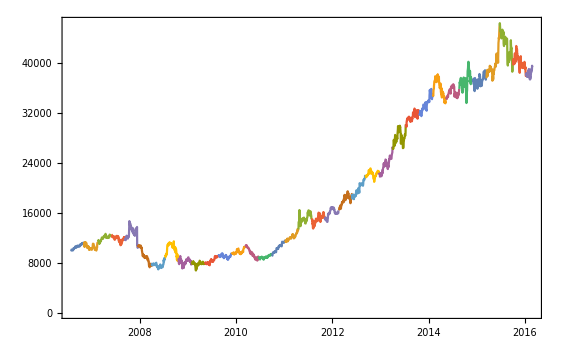
1. The U.S. Healthcare index seeks to track the investment results of healthcare providers, biotechnology companies, and manufacturers of advanced medical devices and pharmaceuticals.

2. GROWTH of 10,000 USD SINCE 31 JULY, 2007.

-Graphics-

### Introduction

This notebook shows the relationship between Markowitz portfolio optimization and Kelly optimization. It is based on the whitepaper by Dr Thomas Starke. All calculation are written in Mathematica 10. 

There are two sections of the demonstration; random data and actual market data. Random data; that will help you to get a idea of how to use this investment strategy for asset allocation and to improve the understanding of the modelling. Then, we shall create a backtest that the asset-weights in a kelly-optimization way.

## Simulations

### Setup Data

Assume that we have 4 assets, each with a return series of 500 observations. We can use NormalDistribution[] to sample returns from a normal distribution.

```mathematica
Remove["Global`*"]

(* Number of Assets *)
numberOfAssets=4;
(* Number of Obserations *)
numberOfObs=500;

vectorOfSimReturns=
RandomVariate[NormalDistribution[],{numberOfAssets,numberOfObs}];
```

Remove::rmnsm: There are no symbols matching "Global`*".

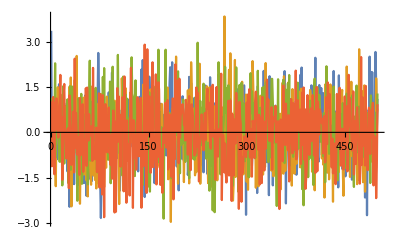

```mathematica
ListLinePlot[vectorOfSimReturns]
```

### Random Weights and the Returns/Risk of Each Portfolio

We can generate a wide range of random weights, which can be used to create different portfolios with a wide range of returns(mean) and risks(standard deviation). We assumed that all capital shall be invested, the sum of the weights is equal to 1.

```mathematica
randomWeights = #/Total[#]& [RandomReal[{0,1},numberOfAssets]]
```

{0.472833,0.299187,0.0935668,0.134413}

```mathematica
Total[randomWeights]
```

1.

### Evaluate how many of these random portfolios would perform

In this section, the goal we are calculating the mean returns as well as the standard deviation (volatility). You can also see that there is a filter that only allows to plot portfolios with a standard deviation of < 1.5 for better illustration.

```mathematica
randomPorfolio[pReturns_] := 
Module[ {expectedReturns, randomWeights, covMatrix, sigma,mu},
expectedReturns= Mean@Transpose@pReturns;
randomWeights = #/Total[#]& [RandomReal[{0,1},Length[pReturns]]];
covMatrix= Covariance[Transpose@pReturns];
mu=randomWeights.expectedReturns;
sigma=Sqrt[randomWeights.covMatrix.randomWeights];

If[sigma > 1.5,randomPorfolio[pReturns], Return[ {sigma,mu}]];
];
```

### Generating the mean returns and volatility for 500 random portfolios:

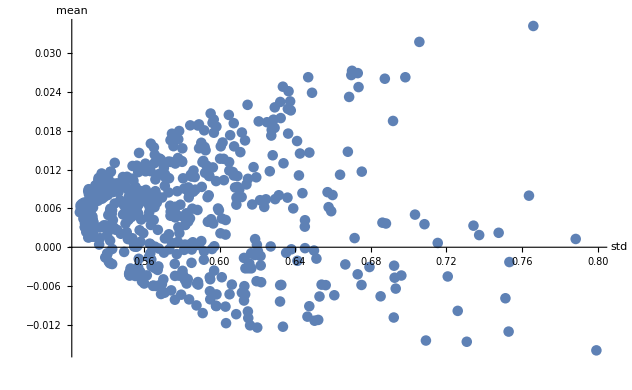

```mathematica
numPortfolios =500;
vectorOfPortfolios = {};
For[i=1,i<numPortfolios ,i++, AppendTo[vectorOfPortfolios,randomPorfolio[vectorOfSimReturns]]];
ListPlot[vectorOfPortfolios,
AxesLabel->{Text["std"],Text["mean"]},
PlotStyle->PointSize[0.012]]
```

### The Efficient Frontier

S.T.    ∑w = 1
          w.avgReturns = tgtReturn
          
where vectorOfWeights is a vector of weights, mS is the sample variance/covariance matrix, optimalReturns is a vector of returns, and muRange is the target return.

The problem is that FindMinimum gives slightly different weights than NMinimize. Both give slightly different weights; I would prefer to use FindMinimum as it is much faster, and it seems to be more accurate.

```mathematica
optimalPorfolio[pReturns_] := 
Module[{mS, vP, vx, x, muRange,  mu, returnRisk, s},
mS=Covariance[Transpose@pReturns];vP=Mean@Transpose@pReturns;vx=Array[x,Length[pReturns]]; 
muRange=10.^(5 Range[0,100,1]/100-1);

s=Monitor[
Table[{#[[1]],vx/.#[[2]]}&[FindMinimum[{-vP.vx+mu vx.mS.vx,
Plus@@vx==1&&And@@Thread[vx≥0]},vx,Method->"QuadraticProgramming"]],{mu,muRange}],mu];
returnRisk={Sqrt[#.mS.#],vP.#}&/@s[[All,2]];
Return[{s[[1,2]],returnRisk}];
]
```

### Optimal Portfolio Weights

{0.22843,0.157709,0.503157,0.110704}

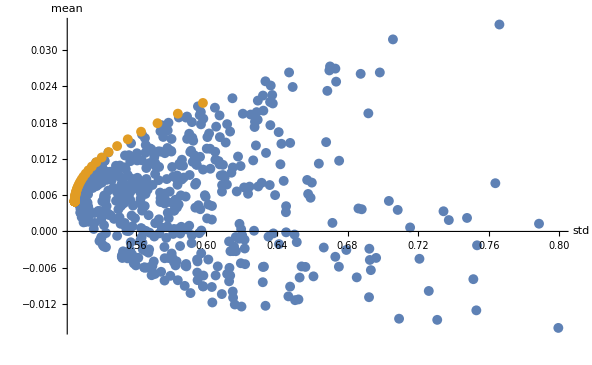

```mathematica
optimalReturns= optimalPorfolio[vectorOfSimReturns];
vectorOfWeights = optimalReturns[[1,All]]
returnRisk = optimalReturns[[2,All]]; 
ListPlot[{vectorOfPortfolios, returnRisk},
AxesLabel->{Text["std"],Text["mean"]},
PlotStyle->PointSize[0.012]
]
```

## Backtesting on real market data

### Retrieve data from Yahoo Finance

```mathematica
(* data = Import["/Volumes/USB/sync/kaggle/frankfurt.csv","HeaderLines"->1 ,"DateStringFormat"->{"Year","-","Month","-","Day"}]; 
Dimensions@data;
A= Transpose@data;
{DimX, DimY} = Dimensions@A;
HistoricalPrices = {};
Do [ HistoricalPrices = Append[HistoricalPrices, {A[[1]][[#]] ,A[[i]][[#]]} & /@Range@DimY]
,{i,2,DimX}]
DateListPlot[HistoricalPrices]
*)
```

### Optimal Portfolio Weights

Assume that we have 20 assets(U.S. Healthcare Sector), each with a return series of  3500 calendar days (2411 trade-days). We can use FinancialData to sample data from a wolfram server.

```mathematica
initCapital =  10000;

Symbols={"JNJ","PFE","MRK","GILD","AGN","UNH","AMGN","MDT","BMY","CELG","LLY","BIIB","TMO","ESRX","AET","CI","SYK","ALXN","BDX","REGN"};

NumberOfSymbols = Length[Symbols];

SampleSize = 3500;
AdjustmentInterval = 70;

StartDate := Date[]-{0,0,SampleSize,0,0,0};
EndDate := Date[];

HistoricalPrices=FinancialData[#,DatePlus[-SampleSize]]&/@Symbols;
```

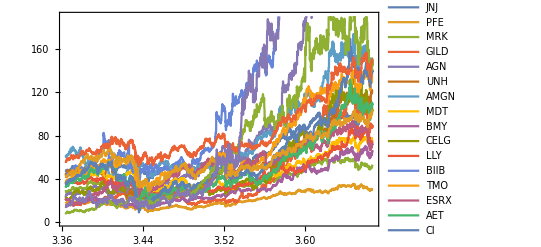

```mathematica
DateListPlot[HistoricalPrices,PlotLegends->{"JNJ","PFE","MRK","GILD","AGN","UNH","AMGN","MDT","BMY","CELG","LLY","BIIB","TMO","ESRX","AET","CI","SYK","ALXN","BDX","REGN"}]
```

### Daily Return of Assets

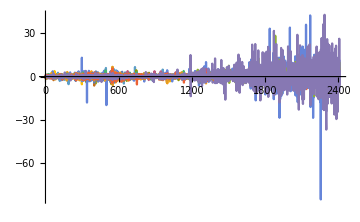

```mathematica
dailyReturns= Differences[Transpose[HistoricalPrices[[#]][[All,2]] & /@Range@Length[Symbols]]];
ListLinePlot[Transpose@dailyReturns,PlotRange->All,ImageSize->Medium]
```

### Kelly Criterion

Initialization PortfolioWeight,  every 70 trade-days update and rebalance its portfolio in a Markowitz-optimal way.

```mathematica
Length[Transpose@HistoricalPrices]
```

2411

```mathematica
data = Partition[HistoricalPrices[[#]],UpTo[AdjustmentInterval]] &  /@ Range@Length[Symbols];
dataReturns = Partition[Differences[HistoricalPrices[[#]][[All,2]]], UpTo[AdjustmentInterval]]& /@ Range@Length[Symbols];
{DimX, DimY} = Dimensions@data;

vectorOfWeights= {};

Do [optimalReturns= optimalPorfolio[dataReturns[[#]][[i]] &/@ Range@Length[Symbols]];
vectorOfWeights = Append[vectorOfWeights, optimalReturns[[1,All]]],{i,DimY}];

vectorOfWeights = Delete[vectorOfWeights,-1];
vectorOfWeights = Insert[vectorOfWeights,Table[N[1/Length[Symbols]],{i,Length[Symbols]}],1];
```

```mathematica
Length[vectorOfWeights]
```

35

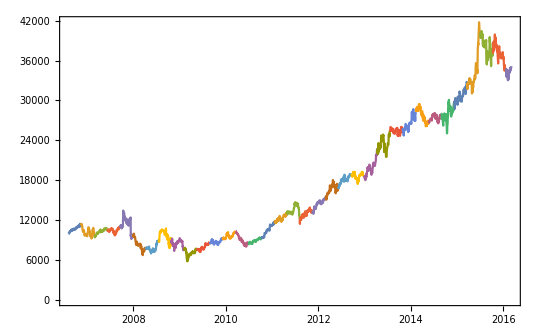

```mathematica
initCash = initCapital;
cashOnHand = {};
stocksOnHand = {};
valueOnMarket= {};

Do[
PortfolioWeight  = vectorOfWeights[[i]];
cashOnHand =  PortfolioWeight * initCash;
stocksOnHand = cashOnHand / Transpose[(data [[#]][[i]][[All,2]]& /@ Range@Length[Symbols])][[1]];
data1 = data[[1]][[i]] [[All, 1]];
data2 = Total[stocksOnHand[[#]]* data[[#]][[i]][[All,2]]  & /@ Range@Length[Symbols]];
valueOnMarket= Append[valueOnMarket, {data1[[#]],data2[[#]]} &/@Range@Length[data1]]; 
initCash = data2[[Length[data2]]];
(* Print[data1[[Length[data2]]],initCash] *)
,{i,DimY}
];

DateListPlot[valueOnMarket]
```

## Conclusions

Even through the 2008 financial crisis, The volatility and return are pretty stable.  This is most likely due to the universe selection and Increasing the number of stocks in the universe might reduce the volatility as well.